```mathematica
(* Import the FEM package *)
Needs["NDSolve`FEM`"]
```

```mathematica
(* define the domain *)
R=Rectangle[{0,0},{1,1}];
```

```mathematica
(* convert to numerical region *)
```

```mathematica
NumRegio = ToNumericalRegion[R]
```

NumericalRegion[FullRegion[2],{{0,1},{0,1}}]

```mathematica
(* Discretize the PDE *)
```

```mathematica
(* Variable data *)
VarData = NDSolve`VariableData[{"DependentVariables"->{u}, "Space"->{x,y}}];
```

```mathematica
(* solution data *)
SolData = NDSolve`SolutionData[{"Space"}->{NumRegio}]
```

{None,NumericalRegion[FullRegion[2],{{0,1},{0,1}}],{},{},{},{},{},{}}

```mathematica
(* define a Helmholtz problem : Δu+λu = 0 *)
Coefficients = {"DiffusionCoefficients"->{{-IdentityMatrix[2]}},"ReactionCoefficients"->{{1}}}
CoeffsPDE = InitializePDECoefficients[VarData,SolData,Coefficients]
```

{DiffusionCoefficients→{{{{-1,0},{0,-1}}}},ReactionCoefficients→{{1}}}

PDECoefficientData[<1,2>]

```mathematica
(* Use Dirichlet BC *)
Subscript[Γ, D]=DirichletCondition[u[x,y]==0, True]
BCs = InitializeBoundaryConditions[VarData,SolData,{{Subscript[Γ, D]}}]
```

DirichletCondition[u[x,y]==0,True]

BoundaryConditionData[<1,2>]

```mathematica
(* Initialize PDE method data -> FEM *)
MethodData = InitializePDEMethodData[VarData,SolData, Method->{"FiniteElement","InterpolationOrder"->2, "MeshOptions"->{  "MaxCellMeasure"->0.01(*,"MaxBoundaryCellMeasure"->0.008*), "NodeReordering"->True, "MeshElementType"->TriangleElement}}]
```

InitializePDEMethodData::femwneo: 2 is not a valid "InterpolationOrder" input. Using default instead.

FEMMethodData[<357,{2},4>]

```mathematica
(* Discretize PDE *)
DiscretePDE = DiscretizePDE[CoeffsPDE,MethodData,SolData];
```

```mathematica
(* Discretize boundary conditions *)
DiscreteBC = DiscretizeBoundaryConditions[BCs, MethodData, SolData];
```

```mathematica
(* retrieve matrices *)
{load,stiffness,damping,mass}=DiscretePDE["SystemMatrices"]
```

{SparseArray[<0>, {357, 1}],SparseArray[<3795>, {357, 357}],SparseArray[<0>, {357, 357}],SparseArray[<0>, {357, 357}]}

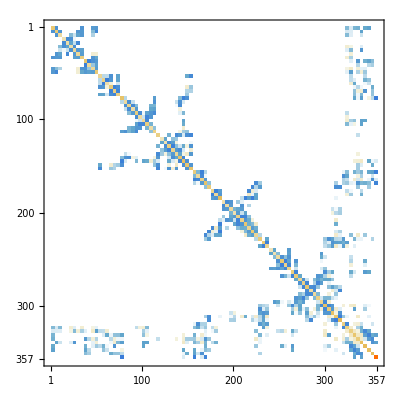

```mathematica
MatrixPlot[stiffness]
```

```mathematica
DeployBoundaryConditions[{load,stiffness,damping,mass}, DiscreteBC]
```

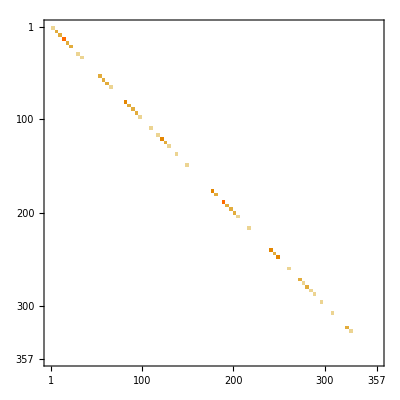

```mathematica
MatrixPlot[mass]
```

```mathematica
MatrixPlot[damping]
```

-Graphics-

```mathematica
{load,stiffness,damping,mass}
```

{SparseArray[<0>, {357, 1}],SparseArray[<3179>, {357, 357}],SparseArray[<80>, {357, 357}],SparseArray[<80>, {357, 357}]}

```mathematica
NumRegio["Properties"]
```

{BoundaryFunction,BoundaryMesh,Bounds,ClearCache,Constraints,ElementMesh,EmbeddingDimension,Predicates,PredicateVariables,Properties,SymbolicRegion}

```mathematica
NumRegio["ElementMesh"]["Properties"]
```

{BoundaryConnectivity,BoundaryElements,Bounds,ContinuousElementConnectivity,Coordinates,ElementConnectivity,EmbeddingDimension,HangingNodes,MeshElements,MeshOrder,PointElements,Properties,Quality,RegionHoles,VertexBoundaryConnectivity,VertexElementConnectivity}

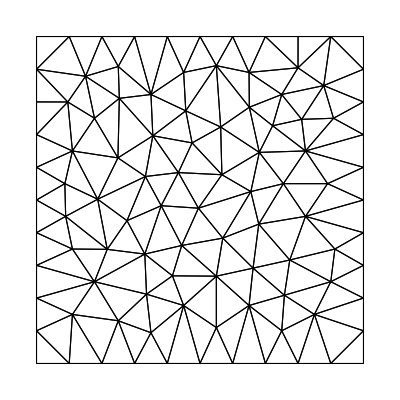

```mathematica
NumRegio["ElementMesh"]["Wireframe"]
```

```mathematica
(* NDEigenvalue *)
```

```mathematica
{L,Bcond}={-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]}
```

{-u^(0,2)[x,y]-u^(2,0)[x,y],DirichletCondition[u[x,y]==0,True]}

```mathematica
SetPrecision[NDEigenvalues[{L,Bcond},u[x,y],{x,y}∈NumRegio, 10,Method->{"SpatialDiscretization"->{"FiniteElement","InterpolationOrder"->2,"MeshOptions"->{  "MaxCellMeasure"->0.0001(*,"MaxBoundaryCellMeasure"->0.008*), "NodeReordering"->True, "MeshElementType"->TriangleElement}}}],10]
```

NDEigenvalues::femwneo: -- Message text not found -- (2) (2)

{19.739209,49.34802528,49.34802529,78.95684816,98.69607034,98.6960709,128.3049129,128.3049134,167.7834063,167.7834081}

```mathematica
Abs[%[[1]]-N[2*Pi^2,10]]
```

2.×10^-7

```mathematica
pos=DiscreteBC["DirichletMatrix"]["NonzeroPositions"][[All,2]];
nDiri=Length[pos];
numEigen=10+nDiri;
```

```mathematica
Eigenvalues[{stiffness,mass},-numEigen]
```

{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
pde = Laplacian[u[x,y],{x,y}]+u[x,y]==0
```

u[x,y]+u^(0,2)[x,y]+u^(2,0)[x,y]==0

```mathematica
{state} = NDSolve`ProcessEquations[{pde,DirichletCondition[u[x,y]==0,True]}, u, Element[{x,y},NumRegio]]
```

{NDSolve`StateData[<SteadyState>]}

```mathematica
femdata=state["FiniteElementData"]
```

FiniteElementData[<1281>]

```mathematica
initCoeffs=femdata["PDECoefficientData"]
```

PDECoefficientData[<1,2>]

```mathematica
initCoeffs["DiffusionCoefficients"]
```

{{{{1,0},{0,1}}}}

```mathematica
initCoeffs["ReactionCoefficients"]
```

{{1}}

```mathematica
initBCs = femdata["BoundaryConditionData"]
```

BoundaryConditionData[<1,2>]

```mathematica
initBCs["Properties"]
```

{All,BoundaryTolerance,Constraints,Discrete,IndexedDiscrete,Nonlinear,Options,Parametric,Properties,ScaleFactor,Stationary,Transient}

```mathematica
methodData = femdata["FEMMethodData"]
vd =methodData["VariableData"]
```

FEMMethodData[<1281,{2},4>]

{None,{x,y},{u},{},{},{},{},{}}

```mathematica
sd=NDSolve`SolutionData[{"Space"->NumRegio}];
```

```mathematica
dpde = DiscretizePDE[initCoeffs, methodData,sd]
```

DiscretizedPDEData[<1281>]

```mathematica
dbc = DiscretizeBoundaryConditions[initBCs,methodData,sd];
```

```mathematica
{load,stiffness,damping,mass}=dpde["SystemMatrices"]
```

{SparseArray[<0>, {1281, 1}],SparseArray[<19121>, {1281, 1281}],SparseArray[<0>, {1281, 1281}],SparseArray[<0>, {1281, 1281}]}

```mathematica
DeployBoundaryConditions[{load,stiffness,damping},dbc]
```

```mathematica
pos = dbc["DirichletMatrix"]["NonzeroPositions"][[All,2]]
nDiri = Length[pos]
numEig=10+nDiri;
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,42,43,63,64,84,85,105,106,126,127,147,148,168,169,189,190,210,211,231,232,252,253,273,274,294,295,315,316,336,337,357,358,378,379,399,400,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,482,503,523,544,564,585,605,626,646,667,687,708,728,749,769,790,810,831,851,872,892,913,933,954,974,995,1015,1036,1056,1077,1097,1118,1138,1159,1179,1200,1220,1241,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281}

160

```mathematica
Eigenvalues[{stiffness,damping},-numEig]
```

{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
{load,stiffness,damping,mass}
```

{SparseArray[<0>, {1281, 1}],SparseArray[<17621>, {1281, 1281}],SparseArray[<160>, {1281, 1281}],SparseArray[<160>, {1281, 1281}]}